```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"};
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"};

If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]

Get["ImageModeling.m"]
```

## 1D test

```mathematica
dim=2^9
gauss1d[x_,sigma_,mu_]:=(1/(Sqrt[2*Pi]*sigma))*Exp[-0.5((x-mu)/sigma)^2];
lambda=1.;
min=-20*lambda;
max=20*lambda;
```

512

```mathematica
arrayGauss1d=Table[gauss1d[x,1,0],{x,min,max,(max-min)/(dim-1)}];
```

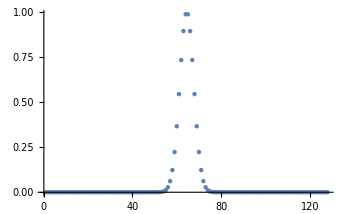

```mathematica
ListPlot[arrayGauss1d*Sqrt[2*Pi],PlotRange->All]
```

Note that the ordering of the output of Fourier appears to be the zero frequency term first, then increasing positive frequency terms, followed by the most negative frequency term, working back on up to the smallest negative frequency term, e.g. 0, 1, 2, 3, 4,-3, -2, -1.

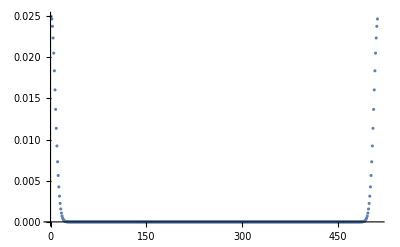

```mathematica
ListPlot[Abs@Fourier[arrayGauss1d,FourierParameters->{1,-1}]/dim,PlotRange->All]
```

Note that this reordering might be off by one, i.e. it should perhaps be #[[dim/2+1;;]]~Join~#[[1;;dim/2]].

```mathematica
Length@(#[[dim/2+2;;]]~Join~#[[1;;dim/2+1]])&[Fourier[arrayGauss1d,FourierParameters->{1,-1}]]
```

512

```mathematica
1/0.025
```

40.

```mathematica
1/Max@(Abs@(#[[dim/2+2;;]]~Join~#[[1;;dim/2+1]])&[Fourier[arrayGauss1d,FourierParameters->{1,-1}]]/dim)
```

40.0783

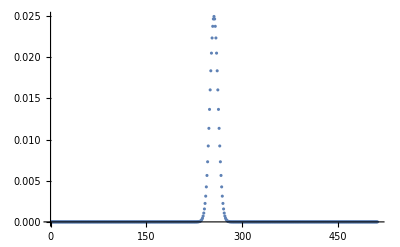

```mathematica
ListPlot[Abs@(#[[dim/2+2;;]]~Join~#[[1;;dim/2+1]])&[Fourier[arrayGauss1d,FourierParameters->{1,-1}]]/dim,PlotRange->All]
```

```mathematica
Sqrt[1/(2*Pi)]//N
```

0.398942

```mathematica
Length@Abs@Fourier[arrayGauss1d,FourierParameters->{1,-1}]
```

256

```mathematica
dim=2^9
lambda=1.;
min=-100*lambda;
max=100*lambda;
width=10*lambda;
pixelSize=((max-min)/(dim-1))/lambda;
Print["Spatial pixel size (lambda) = "<>ToString[pixelSize]];
```

512

Spatial pixel size (lambda) = 0.391389

```mathematica
(max-min)/(dim-1)
```

40/51

```mathematica
targetArrayGauss=Table[Exp[-(x^2+y^2)/width^2],{x,min,max,(max-min)/(dim-1)},{y,min,max,(max-min)/(dim-1)}];
ArrayPlot[%]
Dimensions@targetArrayDot
```

-Graphics-

{256,256}

```mathematica
(targetArrayDot=Table[Boole[(x^2+y^2)≤((max-min)/8)^2],{x,min,max,(max-min)/(dim-1)},{y,min,max,(max-min)/(dim-1)}]);
ArrayPlot[%]
Dimensions@targetArrayDot
```

-Graphics-

{512,512}

## Fourier transforms

```mathematica
ArrayPlot@Fourier[targetArrayDot,FourierParameters->{1,1}]
Dimensions@Fourier[targetArrayDot]
```

-Graphics-

{512,512}

```mathematica
ArrayPlot@Abs@Transpose[RotateLeft[Transpose[RotateLeft[Fourier@targetArrayDot,dim/2]],dim/2]]
```

-Graphics-

```mathematica
ArrayPlot@Abs@Transpose[RotateLeft[Transpose[RotateLeft[Fourier@targetArrayGauss,dim/2]],dim/2]]
```

-Graphics-

```mathematica
ArrayPlot@Abs@InverseFourier@Fourier@targetArrayGauss
```

-Graphics-

```mathematica
ArrayPlot@Abs@rearrange2DFourierArray@Fourier@targetArrayDot
```

-Graphics-

## transfer function

```mathematica
k0p=2*Pi/lambda;
kmin=2*Pi/(max-min)
kmax=2*Pi/pixelSize
```

0.0314159

16.0535

```mathematica
transferArray[delz_]:=Table[opticalTransferFunction[delz,k0p,{kx,ky}],{kx,kmin,kmax,(kmax-kmin)/(dim-1)},{ky,kmin,kmax,(kmax-kmin)/(dim-1)}];
```

```mathematica
ArrayPlot[Arg@transferArray[8],PlotLegends->Automatic]
```

-Graphics-

```mathematica
propField[delz_,target_]:=rearrange2DFourierArray@Fourier[transferArray[delz]*target];
```

```mathematica
ArrayPlot@propField[12,targetArrayDot]
```

-Graphics-

## absorption function

```mathematica
zdim=dim;
sigma0=6*Pi/k0p^2
```

0.477465

```mathematica
chiArray=Table[I*sigma0,{x,min,max,(max-min)/(dim-1)},{y,min,max,(max-min)/(dim-1)},{z,min,max,(max-min)/(dim-1)}];
```

```mathematica
absorption[z0Pix_,z1Pix_]:=Exp[I*(k0p/2)*Total[chiArray[[All,All,z0Pix;;z1Pix]],{3}]];
```

```mathematica
ArrayPlot[(absorption[1,5]*targetArrayGauss),PlotLegends->Automatic]
```

-Graphics-

```mathematica
aArray=Table[a[x,y,z],{x,3},{y,3},{z,3}]
```

{{{a[1,1,1],a[1,1,2],a[1,1,3]},{a[1,2,1],a[1,2,2],a[1,2,3]},{a[1,3,1],a[1,3,2],a[1,3,3]}},{{a[2,1,1],a[2,1,2],a[2,1,3]},{a[2,2,1],a[2,2,2],a[2,2,3]},{a[2,3,1],a[2,3,2],a[2,3,3]}},{{a[3,1,1],a[3,1,2],a[3,1,3]},{a[3,2,1],a[3,2,2],a[3,2,3]},{a[3,3,1],a[3,3,2],a[3,3,3]}}}

```mathematica
aArray[[All,All,1;;2]]
```

{{{a[1,1,1],a[1,1,2]},{a[1,2,1],a[1,2,2]},{a[1,3,1],a[1,3,2]}},{{a[2,1,1],a[2,1,2]},{a[2,2,1],a[2,2,2]},{a[2,3,1],a[2,3,2]}},{{a[3,1,1],a[3,1,2]},{a[3,2,1],a[3,2,2]},{a[3,3,1],a[3,3,2]}}}

```mathematica
Total[aArray,{3}]//TableForm
```

a[1,1,1]+a[1,1,2]+a[1,1,3] | a[1,2,1]+a[1,2,2]+a[1,2,3] | a[1,3,1]+a[1,3,2]+a[1,3,3]
a[2,1,1]+a[2,1,2]+a[2,1,3] | a[2,2,1]+a[2,2,2]+a[2,2,3] | a[2,3,1]+a[2,3,2]+a[2,3,3]
a[3,1,1]+a[3,1,2]+a[3,1,3] | a[3,2,1]+a[3,2,2]+a[3,2,3] | a[3,3,1]+a[3,3,2]+a[3,3,3]